## FeedforwardInputShaping: implements simple input shaping Problem 5.21

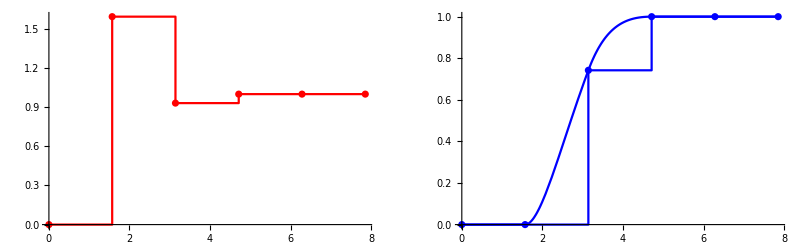

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
SetOptions[Plot,PlotRange -> All];

Ts=π/2;  tmax=5Ts;   ζ=1.0  (* damping *);
(* Ts =0.5; *)
MyInput=UnitStep[t-Ts] (* for step *); 
(* MyInput=UnitStep[t]- UnitStep[t-2Ts] (* for pulse *); MyInput=UnitStep[t-2Ts]- UnitStep[t-4Ts]+UnitStep[t-6Ts]- UnitStep[t-8Ts]+ UnitStep[t-14Ts]- UnitStep[t-16Ts]  (* complex pulses *) ; *)  

G0=1/(s^2+2ζ s +1); G0tf=TransferFunctionModel[G0,s] ; 
G0dtf=ToDiscreteTimeModel[G0tf,Ts,z,Method -> "ZeroOrderHold"];
G0d=Chop[Divide@@G0dtf[[1]]]  (* extract rational polynomial from tf *);  
λ=Denominator[G0d] /.z-> 1  (* scale factor to get unit step response *);
F0d=Denominator[G0d]/(λ z^2)  (*  feedforward filter for reference "input shaping" *);
GF0d = F0d G0d // Simplify;
F0dtf=TransferFunctionModel[F0d,z,SamplingPeriod->Ts];
GF0dtf=TransferFunctionModel[GF0d,z,SamplingPeriod->Ts];

y0d=Quiet@OutputResponse[GF0dtf//N,MyInput,{t,0,tmax}] [[1]] (* output w/ shape *);
r0d=Quiet@OutputResponse[F0dtf//N,MyInput,{t,0,tmax}][[1]] (* shaped input *);

r0dat=Array[{(#-1)*Ts,r0d[[#]]}&,Length[r0d]];
r0dc=Interpolation[r0dat, InterpolationOrder->0] (* cont. staircase sig *);
y0dc=Quiet[OutputResponse[G0tf,r0dc[t-Ts],{t,0,tmax}]](* intersample *); 

py0=Plot[MyInput,{t,0,tmax}];
py0dc=Plot[y0dc,{t,0,tmax},PlotStyle ->{Blue}];py0d=ListPlot[y0d,DataRange->{0,tmax},PlotStyle ->{Blue},Mesh->All];
pr0d=ListPlot[r0dat,PlotStyle ->{Red},Mesh->All];
GraphicsRow[{pr0d,Show[py0d,py0dc]},ImageSize->{400}]
```

```mathematica
{G0dtf,λ,F0dtf,GF0dtf}
```

{(0.161871+0.465584 z)/(0.0432139-0.415759 z+z^2)π/2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.16187081686046640.043213918263772261FalseFalseFalseAutomaticNoneAutomatic,{{0.627455}},(1.59374 (0.0432139-0.415759 z+z^2))/z^2π/2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.5937403855781094$CellContext`z1FalseFalseFalseAutomaticNoneAutomatic,(0.25798+0.74202 z)/z^2π/2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.2579800580770432$CellContext`z1FalseFalseFalseAutomaticNoneAutomatic}

Export data

```mathematica
dat=Table[y0dc,{t,0,tmax,Ts/20}];
(* 
SetDirectory[NotebookDirectory[]];
Export["FeedforwardInputShaping1.dat",dat];
Export["FeedforwardInputShaping1a.dat", {r0d,y0d}ᵀ] ; 
*)
```

## Look at ZOH of G(s) symbolically

```mathematica
G2=1/(s^2+ω^2); G2tf=TransferFunctionModel[G2,s] ;
```

```mathematica
G2dtf=ToDiscreteTimeModel[G2tf,T,z,Method -> "ZeroOrderHold"]//Simplify
```

((-1+ⅇ^(ⅈ T ω))^2 (1+z))/(2 ω^2 (z+ⅇ^(2 ⅈ T ω) z-ⅇ^(ⅈ T ω) (1+z^2)))TTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111$CellContext`z1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
G2d=Chop[Divide@@G2dtf[[1]]]  (* extract rational polynomial from tf *)
```

{{((-1+ⅇ^(ⅈ T ω))^2 (1+z))/(2 (z+ⅇ^(2 ⅈ T ω) z-ⅇ^(ⅈ T ω) (1+z^2)) ω^2)}}

```mathematica
gd0=(1-z^-1)(1/(1-z^-1)-(1-z^-1 Cos[ω T])/(1-2 z^-1 Cos[ω T]+z^-2))//Simplify
```

(2 (1+z) Sin[(T ω)/2]^2)/(1+z^2-2 z Cos[T ω])

## Statespace representations:

```mathematica
{F0dss=StateSpaceModel[F0dtf,SamplingPeriod->Ts],
GF0dss=StateSpaceModel[GF0dtf,SamplingPeriod->Ts]}
```

{0100.0.1.0.0688718-0.6626121.59374π/2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,0100.0.1.0.257980.742020π/2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

## Adding "robustness" against frequency variations:

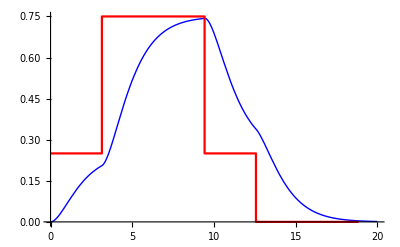

```mathematica
Ts1=π/2;   tmax1=20;MyInput1=UnitStep[t]- UnitStep[t-4Ts];
G1=1/(s^2+1); G1tf=TransferFunctionModel[G1,s] ; 
G1dtf=ToDiscreteTimeModel[G1tf,Ts1,z,Method -> "ZeroOrderHold"];
G1d=Chop[Divide@@G1dtf[[1]]]  (* extract rational polynomial from tf *);  
λ1=Denominator[G1d] /.z-> 1  (* scale factor to get unit step response *);
F1d=(Denominator[G1d]/(λ1 z^2))^2  (*  robust version *);
GF1d = F1d G0d // Simplify;
F1dtf=TransferFunctionModel[F1d,z,SamplingPeriod->Ts1];
GF1dtf=TransferFunctionModel[GF1d,z,SamplingPeriod->Ts1];

y1d=Quiet[OutputResponse[GF1dtf//N,MyInput1,{t,0,tmax1}][[1]]]  (* out w/o shape *);
r1d=Quiet[OutputResponse[F1dtf//N,MyInput1,{t,0,tmax1}][[1]]]  (* shaped input *);

y1dat=Array[{(#-1)*Ts1,y1d[[#]]}&,Length[y1d]];
r1dat=Array[{(#-1)*Ts1,r1d[[#]]}&,Length[r1d]];

r1dc=Interpolation[r1dat, InterpolationOrder->0] (* cont. staircase sig *);
y1dc=Quiet[OutputResponse[G0tf,r1dc[t-Ts1],{t,0,tmax1}]] (* intersample *); 

py1dc=Plot[y1dc,{t,0,tmax1},PlotStyle ->{Blue,Thick}];py1d=ListPlot[y1dat,PlotStyle ->{Blue}];
pr1d=ListPlot[r1dat,PlotStyle ->{Red}];
Show[py1dc,pr1d,ImageSize->{200}]
```

The above works as expected.  In the Robust-Control chapter, we will see that the residual vibration amplitude is linear in the detuning for F0d but quadratic for F1d.